## sector transition plots

### function

```mathematica
Needs["Splines`"];
SetDirectory["/home/julian/mathematica/sector-transition-plots"];

epcg[xy__List,print_:False]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid,curve},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=Splines`SplineFit[pts,Splines`Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};


e[u_]:=initialcurve[u];

If[
print==True,
Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ListPlot[Table[spline[2+(n)i/100],{i,0,100}]],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ParametricPlot[spline[u],{u,2,2+n}]],
Show[
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}]],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ParametricPlot[initialcurve[u],{u,0,2Pi}]]
}}]
]
];
]
```

### plots

```mathematica
size=14;
range={{-w-.2,w+.2},{-lh-1,lh+.4}};
```

#### untwisted plot

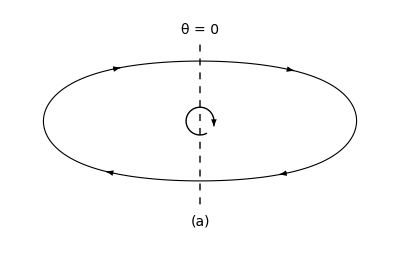

```mathematica
Block[{eplot,h=1.5,t=2.5,w=4.5,thick=.027,thick2=.02,r=.4,lh=2.4},

epcg[{{t,h},{w,0},{t,-h},{-t,-h},{-w,0},{-t,h}},False];

eplot=ParametricPlot[e[u],{u,0,2π},Axes->False,PlotStyle->{Thickness[0.002],Black},PlotRange->range,
Epilog->{
{Arrowheads[thick],Arrow[{e[-π/3],e[-π/3+.05]}]},
{Arrowheads[thick],Arrow[{e[0],e[0+.05]}]},
{Arrowheads[thick],Arrow[{e[2π/3],e[2π/3+.05]}]},
{Arrowheads[thick],Arrow[{e[π],e[π+.05]}]},
{Dashed,Line[{{0,-lh},{0,lh}}]},
{Text[Style["θ = 0",size],{0,1.1lh}]},
{Circle[{0,0},r,{0,5/3π}]},
{Arrowheads[thick2],Arrow[{{0+r,0},{0+r,-.15}}]},
{Text[Style["(a)",size,Italic],{0,-lh-.5}]}
}];
e1=eplot
]
```

#### 1 - fold twisted plot

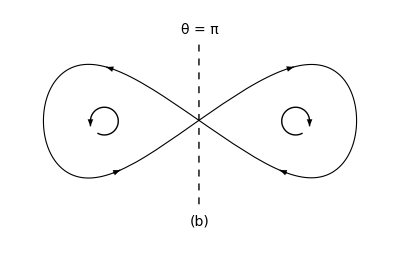

```mathematica
Block[{eplot,h=1.5,t=2.5,w=4.5,m=0,thick=.027,thick2=.02,c=2.75,r=.4,lh=2.4},

epcg[{{t,h},{w,0},{t,-h},{-t,h},{-w,0},{-t,-h}},False];

eplot=ParametricPlot[e[u],{u,0,2π},Axes->False,PlotStyle->{Thickness[0.002],Black},PlotRange->range,
Epilog->{
{Arrowheads[thick],Arrow[{e[-π/3],e[-π/3+.05]}]},
{Arrowheads[thick],Arrow[{e[0],e[0+.05]}]},
{Arrowheads[thick],Arrow[{e[2π/3],e[2π/3+.05]}]},
{Arrowheads[thick],Arrow[{e[π],e[π+.05]}]},
{Circle[{-c,0},r,{4/3π,3π}]},
{Circle[{c,0},r,{0,5/3π}]},
{Arrowheads[thick2],Arrow[{{-c-r,0},{-c-r,-.15}}]},
{Arrowheads[thick2],Arrow[{{c+r,0},{c+r,-.15}}]},
{Dashed,Line[{{-0.03,-lh},{-0.03,lh}}]},
{Text[Style["θ = π",size],{0,1.1lh}]},
{Text[Style["(b)",size,Italic],{0,-lh-.5}]}
}];
e2=eplot
]
```

#### 2 - fold twisted plot

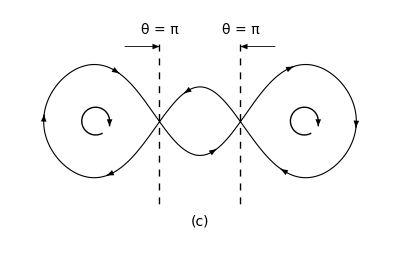

```mathematica
Block[{eplot,h=1.5,t=2.5,w=4.5,m=1,thick=.027,thick2=.02,c=3,r=.4,lh=2.4,lt=1.165},

epcg[{{0,-m},{t,h},{w,0},{t,-h},{0,m},{-t,-h},{-w,0},{-t,h}},False];

eplot=ParametricPlot[e[u],{u,0,2π},Axes->False,PlotStyle->{Thickness[0.002],Black},PlotRange->range,
Epilog->{
{Arrowheads[thick],Arrow[{e[π/2],e[π/2+.05]}]},
{Arrowheads[thick],Arrow[{e[π/4],e[π/4+.05]}]},
{Arrowheads[thick],Arrow[{e[3π/2],e[3π/2+.05]}]},
{Arrowheads[thick],Arrow[{e[π/4+π],e[π/4+π+.05]}]},
{Arrowheads[thick],Arrow[{e[-π/4],e[-π/4+.05]}]},
{Arrowheads[thick],Arrow[{e[-π/4-π],e[-π/4-π+.05]}]},
{Arrowheads[thick],Arrow[{e[0.1],e[0.15]}]},
{Arrowheads[thick],Arrow[{e[π+0.1],e[π+.15]}]},
{Circle[{-c,0},r,{0,5/3π}]},
{Circle[{c,0},r,{0,5/3π}]},
{Arrowheads[thick2],Arrow[{{-c+r,0},{-c+r,-.15}}]},
{Arrowheads[thick2],Arrow[{{c+r,0},{c+r,-.15}}]},
{Dashed,Line[{{-lt,-lh},{-lt,lh}}]},
{Dashed,Line[{{lt,-lh},{lt,lh}}]},
{Arrowheads[thick2],Thickness[.0015],Arrow[{{-lt-1,lh-.25},{-lt,lh-.25}}]},
{Arrowheads[thick2],Thickness[.0015],Arrow[{{lt+1,lh-.25},{lt,lh-.25}}]},
{Text[Style["θ = π",size],{-lt,1.1lh}]},
{Text[Style["θ = π",size],{lt,1.1lh}]},
{Text[Style["(c)",size,Italic],{0,-lh-.5}]}
}];
e3=eplot
]
```

#### 2 - fold twisted plot, pinched

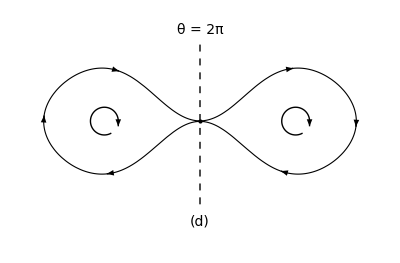

```mathematica
Block[{eplot,h=1.5,t=2.5,w=4.5,m=0,thick=.027,thick2=.02,c=2.75,r=.4,lh=2.4},

epcg[{{0,-m},{t,h},{w,0},{t,-h},{0,m},{-t,-h},{-w,0},{-t,h}},False];

eplot=ParametricPlot[e[u],{u,0,2π},Axes->False,PlotStyle->{Thickness[0.002],Black},PlotRange->range,
Epilog->{
{PointSize[Large],Point[{{0,0}}]},
{Arrowheads[thick],Arrow[{e[π/2],e[π/2+.05]}]},
{Arrowheads[thick],Arrow[{e[π/4],e[π/4+.05]}]},
{Arrowheads[thick],Arrow[{e[3π/2],e[3π/2+.05]}]},
{Arrowheads[thick],Arrow[{e[π/4+π],e[π/4+π+.05]}]},
{Arrowheads[thick],Arrow[{e[-π/4],e[-π/4+.05]}]},
{Arrowheads[thick],Arrow[{e[-π/4-π],e[-π/4-π+.05]}]},
{Circle[{-c,0},r,{0,5/3π}]},
{Circle[{c,0},r,{0,5/3π}]},
{Arrowheads[thick2],Arrow[{{-c+r,0},{-c+r,-.15}}]},
{Arrowheads[thick2],Arrow[{{c+r,0},{c+r,-.15}}]},
{Dashed,Line[{{0,-lh},{0,lh}}]},
{Text[Style["θ = 2π",size],{0,1.1lh}]},
{Text[Style["(d)",size,Italic],{0,-lh-.5}]}
}];
e4=eplot
]
```

#### combined plot

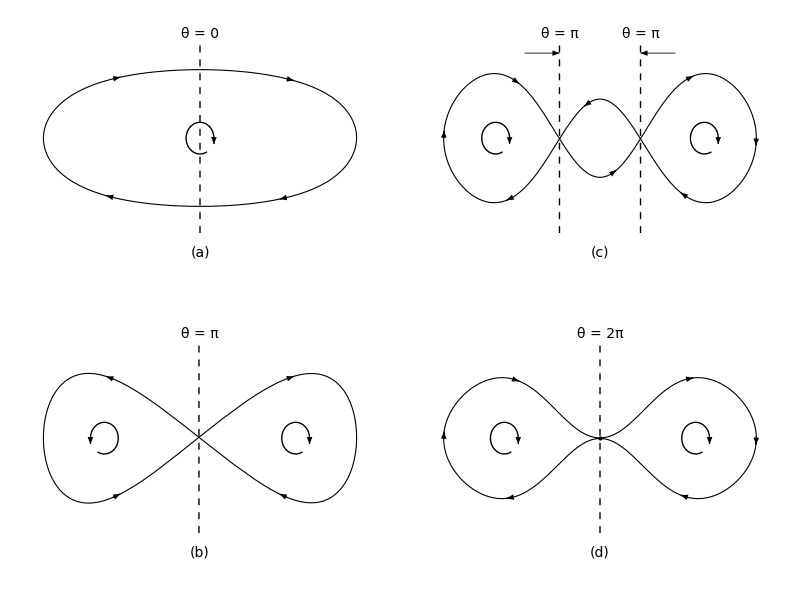

```mathematica
Block[{combiplot},
combiplot=
TableForm[{{e1,e3},{e2,e4}}];
Export["SectorTransitionPlots.eps",combiplot];
Export["/home/julian/latex/CVL-electron/SectorTransitionPlots.eps",combiplot];
combiplot
]
```